## Setup

This setup uses (n,η) as variables.

### PDE Solver

```mathematica
ClearAll@runTwoComponentSim;
Options[runTwoComponentSim]=Join[Options[NDSolve],{"GridPoints"->100,"BC"->"Reflective"}];
runTwoComponentSim[{f_,g_},params_,{uInit_,vInit_},tMax_,opts:OptionsPattern[]]:=First@NDSolve[
{
D[u[x,t],t]==Du/L^2 D[u[x,t],{x,2}]+(f/.{u->u[x,t],v->v[x,t]}),
D[v[x,t],t]==Dv/L^2D[v[x,t],{x,2}]+(g/.{u->u[x,t],v->v[x,t]}),
If[OptionValue["BC"]==="Periodic",
{u[0,t]==u[1,t],v[0,t]==v[1,t],
(D[u[x,t],x]/.x->0)==(D[u[x,t],x]/.x->1),(D[v[x,t],x]/.x->0)==(D[v[x,t],x]/.x->1)},
{(D[u[x,t],x]/.x->0)==0,(D[v[x,t],x]/.x->0)==0,
(D[u[x,t],x]/.x->1)==0,(D[v[x,t],x]/.x->1)==0}],
u[x,0]==uInit[x],v[x,0]==vInit[x]
}/.params,
{u,v},
{x,0,1},{t,0,tMax},
Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->1},"Method"->{"IDA","ImplicitSolver"->"Newton"}}];
```

### Finite difference setup

#### Stationary state equations

```mathematica
discreteLaplace[data_,dx_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,2]/dx^2
]
```

```mathematica
ClearAll@setupFiniteDifferenceEqs;
setupFiniteDifferenceEqs[f_,g_,gridRes_]:=With[{
uVec=Thread[u@Range[gridRes]],
vVec=Thread[v@Range[gridRes]]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"uVec"->uVec,
"vVec"->vVec,
"Vars"->Join[uVec,vVec],
"Eqs"->{
Du/L^2discreteLaplace[uVec,1/gridRes]+(f/.{u->uVec,v->vVec}),
Dv/L^2discreteLaplace[vVec,1/gridRes]+(g/.{u->uVec,v->vVec})
}
|>
]
```

```mathematica
getInitGuess[fdSetup_,params_,initSol_,t_]:=Join[
Transpose[{
fdSetup["uVec"],
u[x,t]/.params/.initSol/.x->fdSetup["UnitGrid"]
}],
Transpose[{
fdSetup["vVec"],
v[x,t]/.params/.initSol/.x->fdSetup["UnitGrid"]
}]
]
```

#### “Glued Jacobian” for antisymmetry of the competition mode

```mathematica
laplaceMatrixAS[n_]:=SparseArray[{
{1,1}->-1,{-1,-1}->-3,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]
Options@constructGluedJacobianAS={"Reverse"->False};
constructGluedJacobianAS[fdSetup_,params_,statSol_,dfdu_,OptionsPattern[]]:=
With[{
solVec=If[OptionValue["Reverse"]===True,Reverse@#,#]&@Transpose[{
fdSetup["uVec"]/.statSol,
fdSetup["vVec"]/.statSol
}],
dfduP=dfdu/.params,
gridRes=Length@statSol/2
},
KroneckerProduct[laplaceMatrixAS[gridRes],{{Du,0},{0,Dv}}/(L/gridRes)^2/.params]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{u,v}->solVec[[i]]]),
{i,gridRes}
]
]
]
```

#### Find stationary state stability

```mathematica
getNumericalEV[fdSetup_,params_,reverse_]:=Block[{u,v,run,sol},
run=runTwoComponentSim[
{f,g},
params,
{
√(2/d)/2(1-Tanh[L(#-p/√(2/d))/(2 √Du)])&,3 √(d/2)-d √(2/d)/2(1-Tanh[L(#-p/√(2/d))/(2 √Du)])&
},
tMax
];
sol=FindRoot[
fdSetup["Eqs"]/.params,
getInitGuess[fdSetup,params,run,tMax]
];
Re@Eigenvalues[Normal@constructGluedJacobianAS[
fdSetup,
params,
sol,
D[{f,g},{{u,v}}],
"Reverse"->reverse
],-1,Method->{"Arnoldi"}][[1]]
];
```

### Model setup

```mathematica
fixedParams=Join[{d->Du/Dv}/.#,#]&@{Du->1/10,Dv->1,p->2};
```

```mathematica
f=u^2 v-u+eps(p-u);
g=-u^2v+u;
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[f,g,200];
```

```mathematica
tMax=5000;
```

### Setup test / usage example

```mathematica
testParams=Join[fixedParams,{eps->10^-12,L->11}];
```

```mathematica
testRun=runTwoComponentSim[
{f,g},
testParams,
{
√(2/d)/2(1-Tanh[L(#-p/√(2/d))/(2 √Du)])&,
3 √(d/2)-d √(2/d)/2(1-Tanh[L(#-p/√(2/d))/(2 √Du)])&
},
tMax
];
```

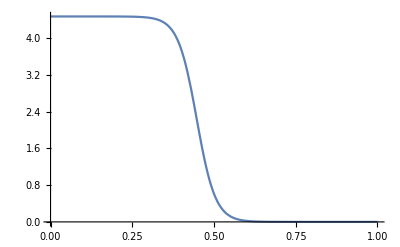

```mathematica
Plot[Evaluate[u[x,tMax]/.testRun],{x,0,1}]
```

```mathematica
testSol=Block[{u,v},FindRoot[
fdSetup["Eqs"]/.testParams,
getInitGuess[fdSetup,testParams,testRun,tMax]
]];//AbsoluteTiming
```

{0.45365,Null}

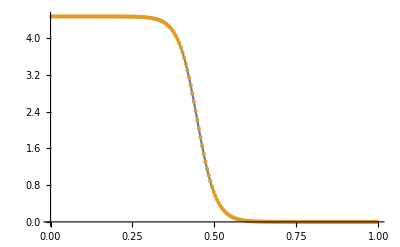

```mathematica
ListPlot[Transpose/@{
{x,u[x,tMax]/.testRun}/.x->fdSetup["UnitGrid"],
{fdSetup["UnitGrid"],fdSetup["uVec"]/.testSol}
},
PlotRange->All,
Joined->{True,False}
]
```

```mathematica
getNumericalEV[
fdSetup,testParams,False
]
```

-8.50365×10^-13

### Data run

```mathematica
newtonIterate[f_,xInit_,dx_]:=Block[{
x0=xInit,r0,r1,maxIt=True
},
Do[
r0=f[x0];PrintTemporary[{x0,r0}];
r1=f[x0+dx];
If[Abs[r0]<Abs[r1-r0],maxIt=False;Break[]];
x0-=dx r0/(r1-r0);,
{5}
];
If[maxIt,Print@"Newton stepper terminated at max number of iterations (5)"];
{x0,r0}
]
```

```mathematica
Off[FindRoot::lstol]
```

```mathematica
epsSweepData=Monitor[
Block[{params,LcritTheory},
Table[
params=Join[{eps->epsIter},fixedParams];
LcritTheory=L/.FindRoot[
eps(2L)/(12 √Du)==(1-ξ)^-2 Exp[-2ξ L/√Du]/.ξ->p/√(2/d)/.params,
{L,0}
];
{
epsIter,
LcritTheory,
newtonIterate[
getNumericalEV[fdSetup,Join[{L->#},params],False]&,
LcritTheory,
0.01
]
},
{epsIter,10^Range[-11,-2,1]}
]],
{N@epsIter,LcritTheory}
];//AbsoluteTiming
```

{8.86899,Null}

#### Theory high res curve

```mathematica
theoryData=Table[
{
epsIter,
{Λ,
(√Du)/(1-d)12/(Λ(1-ξ))Exp[-ξ Λ/√Du]/.ξ->p/√(2/d)
}/.FindRoot[
epsIter Λ/(12 √Du)==(1-ξ)^-2 Exp[-ξ Λ/√Du]/.ξ->p/√(2/d)/.fixedParams,
{Λ,0}
]
},
{epsIter,10^Range[-12,-1,0.5]}
];
```

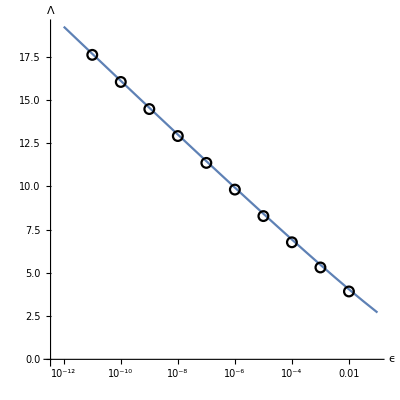

```mathematica
ListLogLinearPlot[{
{#[[1]],#[[2,1]]}&/@theoryData,
{#[[1]],2#[[3,1]]}&/@epsSweepData
},
Joined->{True,False},
AspectRatio->1,
PlotMarkers->{None,{Graphics@{Black,Circle[]},Medium}},
BaseStyle->14,
AxesLabel->{ϵ,Λ}
]
```

```mathematica
Export[NotebookDirectory[]<>"interrupted-coarsening_eps-L-table.txt",{N@#[[1]],2#[[3,1]]}&/@epsSweepData,"Table"]
```

/Users/Fridtjof.Brauns/Mathematica Projects/Coarsening Standalone/interrupted-coarsening_eps-L-table.txt

See mesa-splitting_Brusselator.nb for combined plot with splitting threshold.